```mathematica
nMax[N_]:=N/300*40
```

```mathematica
s[N_,k_]:=nMax[N]/2^k Log[nMax[N]]
```

```mathematica
s[300,1]//N
```

73.7776

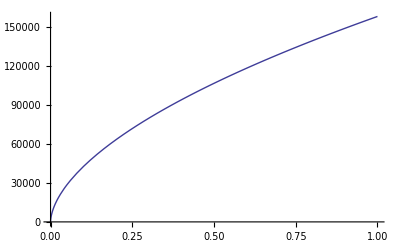

```mathematica
Plot[Sqrt[#]Log[#]&[s[N,10]]/8,{N,1,1000000000000}]
```

```mathematica
Log[10^14]^3//N
```

33498.9

```mathematica
Log[10^15]//N
```

34.5388